```mathematica
kr:=ar*Exp[-br*Abs[t]]*Cos[bi*Abs[t]];
```

```mathematica
ki:=ai*Exp[-br*Abs[t]]*Sin[bi*Abs[t]];
```

```mathematica
Limit[FourierTransform[ki,t,w],w->0]
```

(ai bi √(2/π))/(bi^2+br^2)

```mathematica
Limit[FourierTransform[ki,t,w],w->Infinity]
```

0

```mathematica
Limit[FourierTransform[kr,t,w],w->0]
```

(ar br √(2/π))/(bi^2+br^2)

```mathematica
Limit[FourierTransform[kr,t,w],w->Infinity]
```

0

```mathematica
Limit[FourierTransform[kr+ki,t,w],w->0]
```

((ai bi+ar br) √(2/π))/(bi^2+br^2)

```mathematica
Limit[FourierTransform[kr+ki,t,w],w->Infinity]
```

0

```mathematica
ft:=Evaluate[FourierTransform[kr+ki,t,w]]
```

```mathematica
ft
```

(√(2/π) (ai bi (bi^2+br^2-w^2)+ar br (bi^2+br^2+w^2)))/(bi^4+2 bi^2 (br^2-w^2)+(br^2+w^2)^2)

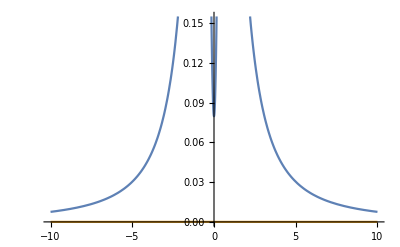

```mathematica
Plot[{ft/.{ar->1,ai->-0.9,br->0.5,bi->0.5},0},{w,-10,10}]
```

```mathematica
extrema:=Simplify[Solve[D[ft,w]==0,w]]
```

```mathematica
For[n=1,n≤Length[extrema],n++,
Print[Solve[Simplify[ft/.extrema][[n]]==0]]]
```

{{br→-(ai bi)/ar},{ai→0,ar→0},{ar→0,bi→0}}

{{ar→(ai bi)/br}}

{{ar→(ai bi)/br}}

{{ar→(ai bi)/br}}

«1 more identical outputs»